```mathematica
f[x_]=√3*Exp[-1/22*x^3 +1/2*x-1/4]
```

√3 ⅇ^(-1/4+x/2-x^3/22)

```mathematica
a=0;b=6;n1=6;n2=10;x0=2.4316;
```

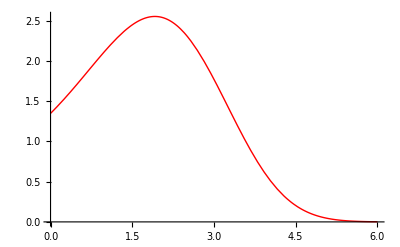

```mathematica
graph=Plot[f[x],{x,a,b},PlotStyle->{Red,Thick}]
```

```mathematica
T1[i_]=Cos[(Pi (2 i+1))/(2 n1+2)];
```

```mathematica
T2[i_]=Cos[(Pi (2 i+1))/(2 n2+2)];
```

```mathematica
data1=Table[{x1=(a+b)/2+(b-a)/2*T1[i],f[x1]},{i,0,n1}]//N//Reverse;
data2=Table[{x2=(a+b)/2+(b-a)/2*T2[i],f[x2]},{i,0,n2}]//N//Reverse;
```

```mathematica
{TableForm[data1],TableForm[data2]}
```

{0.0752163 | 1.40059
0.654506 | 1.84747
1.69835 | 2.52392
3. | 1.77187
4.30165 | 0.310992
5.34549 | 0.0188574
5.92478 | 0.00204604,0.0305357 | 1.36967
0.271104 | 1.54335
0.732751 | 1.91133
1.37808 | 2.38544
2.1548 | 2.51414
3. | 1.77187
3.8452 | 0.696047
4.62192 | 0.152948
5.26725 | 0.0244891
5.7289 | 0.00459502
5.96946 | 0.00168666}

```mathematica
diftab1=Array[dif1,{n1+1,n1+1},{0,0}];
```

```mathematica
For[k=1,k≤n1,k++,For[i=n1,i≥n1-k,i--,dif1[i,k]=""]]
```

```mathematica
For[i=0,i≤n1,i++,dif1[i,0]=data1[[i+1,2]]]
```

```mathematica
For[k=1,k≤n1,k++,For[i=0,i≤n1-k,i++,dif1[i,k]=(dif1[i+1,k-1]-dif1[i,k-1])/(data1[[i+1+k,1]]-data1[[i+1,1]])]]
```

```mathematica
PaddedForm[TableForm[diftab1],{n1,n1-1}]
```

1.40059 |  0.77142 | -0.07601 | -0.15270 |  0.05646 | -0.00789 | -0.00087
 1.84747 |  0.64804 | -0.52262 |  0.08594 |  0.01490 | -0.01296 | 
 2.52392 | -0.57777 | -0.20918 |  0.15584 | -0.05343 |  | 
 1.77187 | -1.12232 |  0.35918 | -0.06997 |  |  | 
 0.31099 | -0.27986 |  0.15454 |  |  |  | 
 0.01886 | -0.02902 |  |  |  |  | 
 0.00205 |  |  |  |  |  |

```mathematica
(*таблица для значение n=10*)
diftab2=Array[dif2,{n2+1,n2+1},{0,0}];
```

```mathematica
For[k=1,k≤n2,k++,For[i=n2,i≥n2-k,i--,dif2[i,k]=""]]
```

```mathematica
For[i=0,i≤n2,i++,dif2[i,0]=data2[[i+1,2]]]
```

```mathematica
For[k=1,k≤n2,k++,For[i=0,i≤n2-k,i++,dif2[i,k]=(dif2[i+1,k-1]-dif2[i,k-1])/(data2[[i+1+k,1]]-data2[[i+1,1]])]]
```

```mathematica
PaddedForm[TableForm[diftab2],{n2,n2-1}]
```

1.369673907 |  0.721921984 |  0.107070357 | -0.121298293 | -0.028804062 |  0.018966831 | -0.000541808 | -0.001575004 |  0.000526234 | -0.000065734 | -0.000011560
 1.543345480 |  0.797108459 | -0.056384172 | -0.182485801 |  0.027517266 |  0.016900018 | -0.007773262 |  0.001180731 |  0.000151659 | -0.000134387 | 
 1.911328418 |  0.734692673 | -0.400132368 | -0.107394043 |  0.087919515 | -0.016920032 | -0.001874160 |  0.002008456 | -0.000614128 |  | 
 2.385444901 |  0.165684018 | -0.643621376 |  0.166250733 |  0.022114614 | -0.025418404 |  0.008160376 | -0.001207555 |  |  | 
 2.514135784 | -0.878219942 | -0.233460846 |  0.237987112 | -0.076741911 |  0.010085911 |  0.002616023 |  |  |  | 
 1.771866334 | -1.272861069 |  0.353681946 | -0.000867973 | -0.040693921 |  0.020065155 |  |  |  |  | 
 0.696047124 | -0.699216379 |  0.351714035 | -0.111917452 |  0.018888841 |  |  |  |  |  | 
 0.152948434 | -0.199061066 |  0.140895319 | -0.071792517 |  |  |  |  |  |  | 
 0.024489099 | -0.043093676 |  0.044151897 |  |  |  |  |  |  |  | 
 0.004595021 | -0.012089525 |  |  |  |  |  |  |  |  | 
 0.001686664 |  |  |  |  |  |  |  |  |  |

```mathematica
(*Построим интерполяционные многочлены Ньютона для неравноотстоящих узлов при n1=6 и n2=10.
Введём вспомогательные многочлены P(x) и построим интерполяционные многочлены с их помощью:*)
P1[x_]=1;P2[x_]=1;Pnr1[x_]=dif1[0,0];Pnr2[x_]=dif2[0,0];
```

```mathematica
For[i=0,i<n1,i++,P1[x_]=P1[x] (x-data1[[i+1,1]]);Pnr1[x_]=Pnr1[x]+dif1[0,i+1] P1[x]]
```

```mathematica
Pnr1[x]//Simplify
```

1.36926+0.352109 x+0.896364 x^2-0.52737 x^3+0.0603354 x^4+0.00520031 x^5-0.000868101 x^6

```mathematica
For[i=0,i<n2,i++,P2[x_]=P2[x] (x-data2[[i+1,1]]);Pnr2[x_]=Pnr2[x]+dif2[0,i+1] P2[x]]
```

```mathematica
Pnr2[x]//Simplify
```

1.34947+0.652649 x+0.304845 x^2-0.344528 x^3+0.306606 x^4-0.187352 x^5+0.0438569 x^6+0.000163285 x^7-0.0016443 x^8+0.000246737 x^9-0.0000115599 x^10

```mathematica
graph1D=ListPlot[data1,PlotStyle->{Darker,PointSize[0.02]}];
```

```mathematica
graph2D=ListPlot[data2,PlotStyle->{Darker,PointSize[0.02]}];
```

```mathematica
graph1Pnr=Plot[Pnr1[x],{x,a,b}];
```

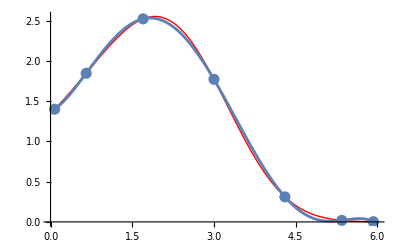

```mathematica
Show[graph,graph1D,graph1Pnr]
```

```mathematica
(*graph2Pnr=Plot[Pnr2[x],{x,a,b}];*)
graph2Pnr=Plot[Pnr2[x],{x,a,b}];
```

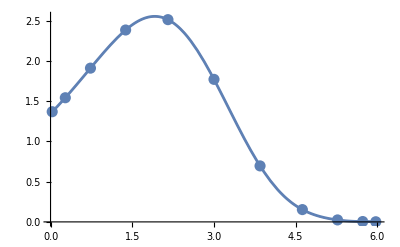

```mathematica
Show[graph,graph2D,graph2Pnr]
```

```mathematica
(*в
Интерполирующие функции функции f(x) при n1=6 и n2=10,построенные встроенной функцией пакета Mathematica*)
Intf1=Interpolation[data1]
```

InterpolatingFunction[…]

```mathematica
Intf2=Interpolation[data2]
```

InterpolatingFunction[…]

```mathematica
(*изобразим полученные интерполяционные функции*)
(*n=6*)
graph1Intf=Plot[Intf1[x],{x,a,b}];
```

InterpolatingFunction::dmval: Input value {0.000122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

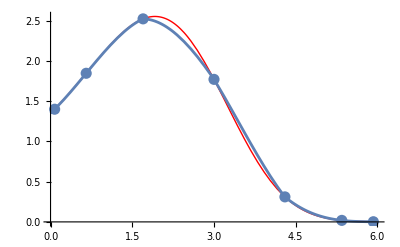

```mathematica
(*n=6*)
Show[graph,graph1D,graph1Intf]
```

InterpolatingFunction::dmval: Input value {0.000122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

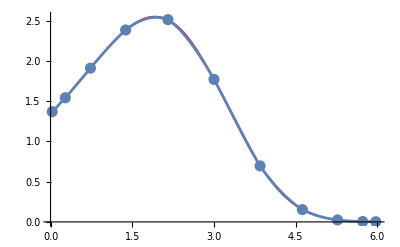

```mathematica
(*n=10*)
graph2Intf=Plot[Intf2[x],{x,a,b}];
Show[graph,graph2D,graph2Intf]
```

```mathematica
(*г*)
```

```mathematica
(*Значения интерполяционных многочленов Ньютона для неравноотстоящих узлов в точке x0:*)
Print["Pnr1[x0]=",Pnr1[x0],", Pnr2[x0]=",Pnr2[x0]]
```

Pnr1[x0]=2.31516, Pnr2[x0]=2.36563

```mathematica
(*Значения интерполирующих функций в точке x0:*)
Print["Intf1[x0]=",Intf1[x0],", Intf2[x0]=",Intf2[x0]]
```

Intf1[x0]=2.25443, Intf2[x0]=2.34475

```mathematica
(*д*)
(*Исследуем погрешность интерполяционного многочлена Ньютона 
для неравноотстоящих узлов и интерполирующей функции при n=6.*)
Rnp1[x_]=Abs[f[x]-Pnr1[x]]//Simplify;
```

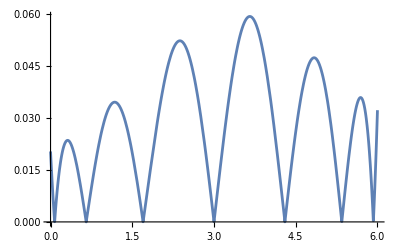

```mathematica
(*График погрешности Rnp1(x):*)
graphErrp1=Plot[Rnp1[x],{x,a,b},PlotRange->Full]
```

```mathematica
(*Как видно из графика,вблизи правой границы отрезка функция 
может принимать столь малые значения,их невозможно вычислить машинно,поэтому ограничим границы поиска максимума в соответствии с графиком::*)
maxErrp1=FindMaximum[Rnp1[x],{x,3,4}]
```

{0.0593069,{x→3.65707}}

```mathematica
(*Результат,полученный функцией FindMaximum,соответствует графику.*)
```

```mathematica
RnI1[x_]=Abs[f[x]-Intf1[x]]//Simplify;
```

```mathematica
(*График погрешности RnI1(x):*)
```

InterpolatingFunction::dmval: Input value {0.000122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

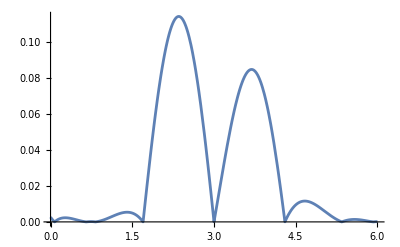

```mathematica
graphErrI1=Plot[RnI1[x],{x,a,b},PlotRange->Full]
```

```mathematica
(*Как видно из графика,вблизи левой границы отрезка функция может принимать столь малые значения,их невозможно вычислить машинно,поэтому ограничим границы поиска максимума в соответствии с графиком::*)
maxErrI1=FindMaximum[RnI1[x],{x,2,3}]
```

{0.114477,{x→2.35307}}

```mathematica
(*Результат,полученный функцией FindMaximum,соответствует графику.*)
```

```mathematica
(*Аналогимчным образом исследуем погрешность 
интерполяционного многочлена Ньютона 
для неравноотстоящих узлов и интерполирующей функции при n=10.*)
```

```mathematica
Rnp2[x_]=Abs[f[x]-Pnr2[x]]//Simplify;
```

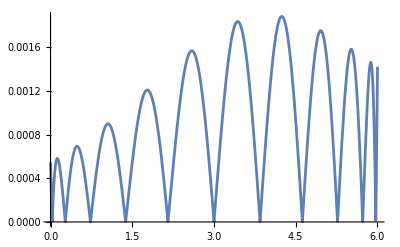

```mathematica
(*График погрешности Rnp2(x):*)
graphErrp2=Plot[Rnp2[x],{x,a,b},PlotRange->Full]
```

```mathematica
(*Так как в некоторых точках отрезка функия может принимать настолько малые значения,что они не могут быть вычислены машинно,ограничим границы поиска максимума в соответствии с графиком:*)
maxErrp2=FindMaximum[Rnp2[x],{x,4,5}]
```

{0.00188399,{x→4.2436}}

```mathematica
RnI2[x_]=Abs[f[x]-Intf2[x]]//Simplify;
```

InterpolatingFunction::dmval: Input value {0.000122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

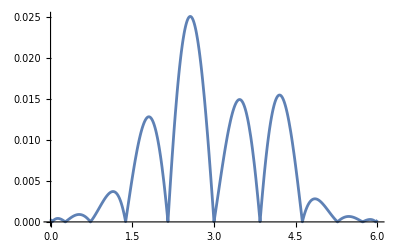

```mathematica
(*График погрешности RnI2(x):*)
graphErrI2=Plot[RnI2[x],{x,a,b},PlotRange->Full]
```

```mathematica
(*Как видно из графика,
точки отрезка функция погрешности столь малые значения,
их невозможно вычислить машинно,следовательно,ограничим границы поиска максимума в соответствии с графиком::*)
```

```mathematica
maxErrI2=FindMaximum[RnI2[x],{x,2.5,3}]
```

{0.025035,{x→2.56435}}